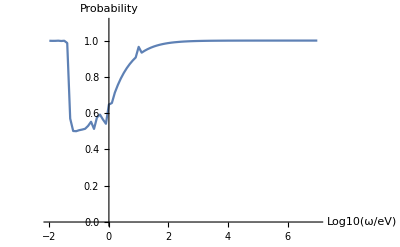

3.041877

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];


omegaVal={};

lowerBound =-2;
upperBound =7;
step =0.1;

t = Table[


(*Параметры АЛП*)
ω=10^(k);
g=6*10^(-20);
m=10^(-8);

(*Конфигурация поля*)
angle = Pi/6;
BSurf = 10^13;
R0 = 10;
period =3;

(*Размер области, должен быть равен радиусу*)
startingPoint = R0;

(*Радиус светового цилиндра*)
upperLimit=47713*period;


(*Значения поля (диполь)*)
bRep={bRad->BSurf*Cos[angle]*(R0/(x+startingPoint))^3,
	bTheta->0.5*BSurf*Sin[angle]*(R0/(x+startingPoint))^3,
	bPhi->0};

(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaPlasma:=3.1*10^(-12)*(bRad*Cos[angle]-bTheta*Sin[angle])*(1/period)*(1/ω);

deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,deltaMPhi},
	{deltaMTheta,deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
r[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)r0={{r11[0]==1/2,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1/2,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};



(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ r'[x]==r[x].mat-mat.r[x]},r0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];
Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]
,{k,lowerBound,upperBound,step}];

(*Строим график*)
data=Transpose[{Range[lowerBound,upperBound,step],t}];
plot = ListLinePlot[data,PlotRange->{{lowerBound,upperBound},{0.0,1.1}},AxesLabel->{"Log10(ω/eV)","Probability"}, PlotMarkers->None]
AbsoluteTime[]-time

(*dataToFile = Transpose[{10^x/.x->Range[lowerBound,upperBound,step],t}];
Export["Mixing_15.dat",dataToFile,"Table"]*)
```

0.647492

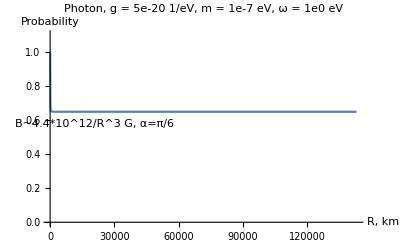

0.299168

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

(*Параметры АЛП*)
ω=10^(0);
g=6*10^(-20);
m=10^(-8);

(*Конфигурация поля*)
angle = Pi/6;
BSurf = 10^13;
R0 = 10;
period =3;

(*Размер области, должен быть равен радиусу*)
startingPoint = R0;

(*Радиус светового цилиндра*)
upperLimit=47713*period;


(*Значения поля (диполь)*)
bRep={bRad->BSurf*Cos[angle]*(R0/(x+startingPoint))^3,
	bTheta->0.5*BSurf*Sin[angle]*(R0/(x+startingPoint))^3,
	bPhi->0};

(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaPlasma:=3.1*10^(-12)*(bRad*Cos[angle]-bTheta*Sin[angle])*(1/period)*(1/ω);

deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,deltaMPhi},
	{deltaMTheta,deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
r[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)r0={{r11[0]==1/2,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1/2,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};

(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ r'[x]==r[x].mat-mat.r[x]},r0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];

Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]
p1=Plot[Re[Evaluate[{r11[x]+r22[x]}/.eqs]],{x,0,upperLimit},PlotRange->{{0,upperLimit},{0.0,1.1}},PlotLabel->"Photon, g = 5e-20 1/eV, m = 1e-7 eV, ω = 1e0 eV", AxesLabel->{"R, km","Probability"},PlotLabels->Placed["B~4.4*10^12/R^3 G, α=π/6", Left]]
AbsoluteTime[]-time
```

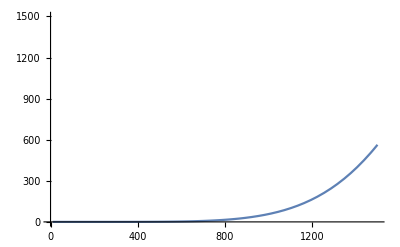

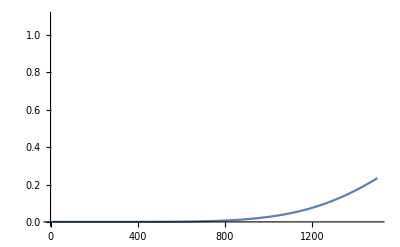

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];



(*Параметры*)
ω=100;
g=6*10^(-20);
lowerLimit = 0;
upperLimit=1500;
m=10^(-9);
angle = Pi/3;
startingPoint =10;

bSurf=10^15;

bRep={brad->1*bSurf*(10/(x+startingPoint))^3,btr->3.1*bSurf*(10/(x+startingPoint))^3,bparal->0};

deltaMtr:=5.0*10^(-12)*btr*(g/10^(-19));
deltaMparal:=5.0*10^(-12)*bparal*(g/10^(-19));
deltaMass:=2.5*10^(-5)*(m/10^(-7))^2*(1/ω);
deltaPlasma:=3.8*10^(-12)*(btr)*(1/ω);
deltaCEDtr:=-1.2*10^(-22)*(ω)*btr^2;
deltaCEDparal:=-1.2*10^(-22)*(ω)*bparal^2;

probability:=4deltaMtr^2/((deltaCEDtr+deltaMass-deltaPlasma)^2+4deltaMtr^2);
oscLen:=2Pi/Sqrt[(deltaCEDtr+deltaMass-deltaPlasma)^2+4deltaMtr^2];

Plot[oscLen/.bRep,{x,startingPoint,1500}, PlotRange->{{0,upperLimit},{0.0,upperLimit}}]
Plot[probability/.bRep,{x,startingPoint,1500}, PlotRange->{{0,upperLimit},{0.0,1.1}}]
```